```mathematica
ClearAll["Global`*"]
```

The Jacobian at the internal steady state

```mathematica
Jac = ({{λ-(1-R) σ, R ρ, H ρ+F σ}, {(1-R) σ, -μ-R ρ, -H ρ-F σ}, {-m R, -R ρ, -F m+(1-R) α-R α-H ρ}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
JacSpecSol//MatrixForm
```

((λ ρ (λ-σ))/(λ ρ+μ σ) | (μ ρ (-λ+σ))/(λ ρ+μ σ) | (α λ (μ+ρ))/(m μ+λ ρ)
(λ (μ+ρ) σ)/(λ ρ+μ σ) | -(μ (μ+ρ) σ)/(λ ρ+μ σ) | -(α λ (μ+ρ))/(m μ+λ ρ)
(m μ (λ-σ))/(λ ρ+μ σ) | (μ ρ (λ-σ))/(λ ρ+μ σ) | (α μ (λ-σ))/(λ ρ+μ σ))

```mathematica
TCMHfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,γ_,ζ_,f0_,mm0_] :=(
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,σ];


growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts* ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*B0*M^η;
resourcegrowth = 0.5;

TC = N[growth];
ValueSigma = N[starvation];
Hopf = N[HopfAnalytic/.{λ->growth,ρ->recovery,μ->mortality,m->maintenance,α->resourcegrowth}];
{TC,ValueSigma,Re[(σ/.Hopf)[[2]]],growth}
)
```

```mathematica
TCMHfunc[
10^6,
10,
1.9*10^(-2),
0.0245,
21.39/2*1000(*J/gram*),
3/4,
-0.206,
3.3879*10^(-7),
1.19,
1.01,
0.0202,
0.324
]
```

{0.210829,72.0692,101.057,0.210829}

```mathematica
TCMHfunc[
10^5,
10,
1.9*10^(-2),
0.0245,
21.39/2*1000(*J/gram*),
3/4,
-0.206,
3.3879*10^(-7),
1.19,
1.01,
0.0202,
0.324
]
```

{0.0210829,7.20692,0.267063,0.0210829}

```mathematica
SigmaOutput=ParallelTable[
TCMHfunc[
1,
RandomReal[{0.1,10^6}],
1.9*10^(-2),
0.0245,
21.39/2*1000(*J/gram*),
3/4,
-0.206,
3.3879*10^(-7),
1.19,
1.01,
0.0202,
0.324
],{100}];
```

$Aborted

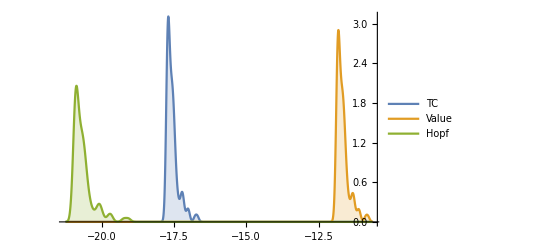

```mathematica
SmoothHistogram[{Log[SigmaOutput[[All,1]]],Log[SigmaOutput[[All,2]]],Log[SigmaOutput[[All,3]]]},PlotLegends->{"TC","Value","Hopf"},Filling->Bottom]
```

```mathematica
HopfPlot[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,γ_,ζ_,f0_,mm0_] := (
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];


growth =N[ts* λ0*M^η2];
(*starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];*)
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
(*recovery =N[ ts* ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];*)
maintenance = B0*M^η;
resourcegrowth = 0.5;


HopfAllometric=HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};
ρ/.HopfAllometric
)
```

```mathematica
curve=ParallelTable[
HopfPlot[
1,
RandomReal[{0.1,10^6}],
1.9*10^(-2),
0.0245,
21.39/2*1000(*J/gram*),
3/4,
-0.206,
3.3879*10^(-7),
1.19,
1.01,
0.0202,
0.324
],{10}];
```

```mathematica
curve
```

{{-(101512. (1.89013×10^-11-0.000816135 σ-2.46277×10^-6 σ^2))/σ-1/2 √((4.12185×10^10 (1)^2)/σ^2-(7.57033×10^20 (1))/σ+1/(3 1)+1/(1^2 1)+(2.00286×10^20 (1)^(1/3))/(2.31596×10^-8 σ-σ^2))-1/2 √1,1,1,1}}
 |  |  |  |

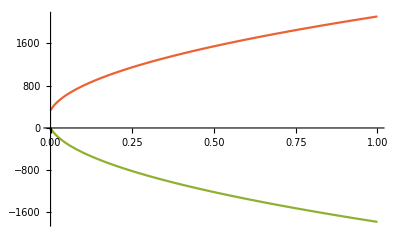

```mathematica
Plot[curve,{σ,0,1},PlotRange->{0,All}]
```